# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\Chaotic_eigenfunctions\Spectral rigidity

```mathematica
(*Operators*)
Clear[Sz,SM,Sm,Sx,Sy];
Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);
Clear[Floq];
Floq[J_,α_,k_,τ_]:=N[MatrixExp[(-I*k/(2J))(Sx[J].Sx[J])].MatrixExp[(-I*α*τ)(Sz[J])]];
Clear[a2];
a2[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# Method

```mathematica
Clear[haar];
haar[dim_Integer]:=Module[{l=2*dim+1,state1},
state1=Table[RandomReal[NormalDistribution[],2],{l}];
Normalize[state1[[All,1]]+I state1[[All,2]]]
];
```

```mathematica
Clear[J];
J=500;
α=0.84;
τ=1;
```

```mathematica
rotation=MatrixExp[I(N[Pi])Sx[J]];
rotation2=MatrixExp[I(N[α/2])Sz[J]];
rotation3=MatrixExp[I(N[-α/2])Sz[J]];
```

```mathematica
k=23.;
(*North pole*)
(*mat=ConjugateTranspose[rotation2].Floq[J,α,k,τ].rotation2;*)
(*South pole*)
(*mat=ConjugateTranspose[rotation3].ConjugateTranspose[rotation].Floq[J,α,k,τ].rotation.rotation3;*)
mat=Floq[J,α,k,τ];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Eigensystem[matM];
{eigenvalm,eigenvecm}=Eigensystem[matm];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
eigenval=Riffle[eigenvalM,eigenvalm];
eigenvec=Riffle[neweigenvecM,neweigenvecm];
```

# Unfolding

```mathematica
(*Generate COE matrix*)
n=100; (*Matrix size*)
randomMatrix=Orthogonalize[RandomVariate[NormalDistribution[],{n,n}]];
eigenvalues=Eigenvalues[randomMatrix];
eigenAngles=Arg[eigenvalues]; (*Extract eigenvalue angles*)
sortedAngles=Sort[eigenAngles];
```

```mathematica
(*Unfold spectrum to unit density*)
unfoldedSpectrum=Rescale[sortedAngles,{0,2 Pi},{0,Length[sortedAngles]}];
```

```mathematica
(*Function to calculate Delta3 for a single interval*)delta3[interval_]:=Module[{x,nLevels,fit,residuals,intervalLength},intervalLength=Length[interval];
nLevels=Range[1,intervalLength];(*Corresponding level indices*)fit=FindFit[Transpose[{nLevels,interval}],a+b x,{a,b},x];(*Linear fit*)residuals=interval-(a+b nLevels/. fit);(*Deviations from fit*)Total[residuals^2]/intervalLength (*Mean squared deviation*)];

(*Calculate Delta3 for given L*)
calculateDelta3[unfoldedSpectrum_,l_]:=Module[{intervals,delta3Values},intervals=Table[Take[unfoldedSpectrum,{i,Min[i+l-1,Length[unfoldedSpectrum]]}],{i,1,Length[unfoldedSpectrum]-l+1}];
delta3Values=delta3/@intervals;
Mean[delta3Values] (*Average Delta3 for all intervals of length L*)];
```

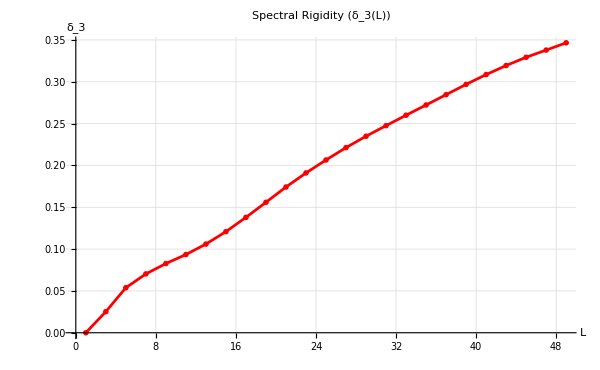

```mathematica
(*Range of L values*)
(*Adjust range and step size as needed*)
lRange=Range[1,50,2]; 
(*Compute Delta3(L) for each L*)
delta3ValuesForL=Table[calculateDelta3[unfoldedSpectrum,l],{l,lRange}];
(*Plot Delta3(L)*)
ListPlot[Transpose[{lRange,delta3ValuesForL}],PlotStyle->{Red,PointSize[Large]},PlotMarkers->"OpenMarkers",Joined->True,PlotLabel->"Spectral Rigidity (δ_3(L))",AxesLabel->{"L","δ_3"},GridLines->Automatic,ImageSize->600]
```

# Spectral statistics

## COE

```mathematica
dim=201;
p=50;
args=RandomVariate[MatrixPropertyDistribution[Arg[Eigenvalues[x]],x\[Distributed]CircularOrthogonalMatrixDistribution[dim]],p];
```

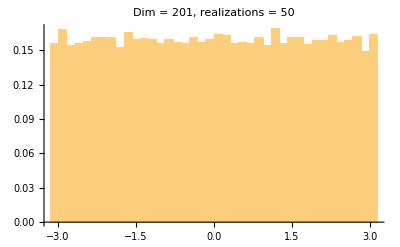

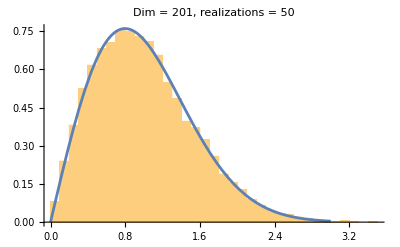

```mathematica
Histogram[Join@@args,{-Pi,Pi,2 Pi/40},PDF,PlotLabel->Style["Dim = "<>ToString[dim]<>", realizations = "<>ToString[p],Black,20]]
diffs=Join@@Map[Composition[Differences,Sort],args/(2 Pi) dim];
WignerSurmisePDF[x_,β:1]:=(Pi/2) x Exp[(-Pi/4) x^2];
Show[Histogram[diffs,{0.1},PDF],Plot[WignerSurmisePDF[x,1],{x,0,3}],PlotLabel->Style["Dim = "<>ToString[dim]<>", realizations = "<>ToString[p],Black,20]]
```

## QKT test

```mathematica
J=200;
dim=J+1;
α=0.84;
τ=1;
p=50;
k=15.;
klist=RandomReal[{k-0.001,k+0.001},p];
```

```mathematica
matrices=ParallelTable[Floq[J,α,k,τ],{k,klist}];
matricesM=Table[k[[i,j]],{k,matrices},{i,1,2J+1,2},{j,1,2J+1,2}];
eigenvals=ParallelTable[Eigenvalues[i],{i,matricesM}];
args=Arg[eigenvals];
```

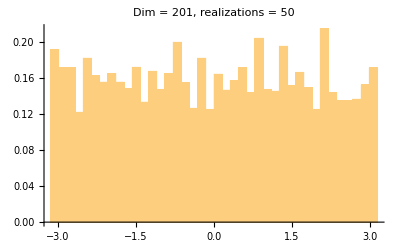

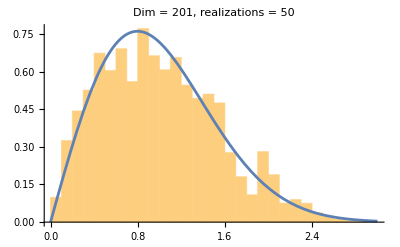

```mathematica
Histogram[Join@@args,{-Pi,Pi,2 Pi/40},PDF,PlotLabel->Style["Dim = "<>ToString[dim]<>", realizations = "<>ToString[p],Black,20]]
diffs=Join@@Map[Composition[Differences,Sort],args/(2 Pi) dim];
Show[Histogram[diffs,{0.1},PDF],Plot[WignerSurmisePDF[x,1],{x,0,3}],PlotLabel->Style["Dim = "<>ToString[dim]<>", realizations = "<>ToString[p],Black,20],PlotRange->All]
```

```mathematica
args//Dimensions
```

{50,201}

```mathematica
eigenvals//Dimensions
```

{50,201}

```mathematica
eigenvalues=eigenvals[[1]];
```

```mathematica
sortedEigenvalues=Sort[Arg[eigenvalues]];
unfoldedSpectrum=Rescale[sortedEigenvalues,{0,2 Pi},{0,Length[sortedEigenvalues]}];
(*cumulativeDensity=Rescale[Range[Length[sortedEigenvalues]],{1,Length[sortedEigenvalues]},{0,Length[sortedEigenvalues]}];*)
(*unfoldedSpectrum=cumulativeDensity;*)
```

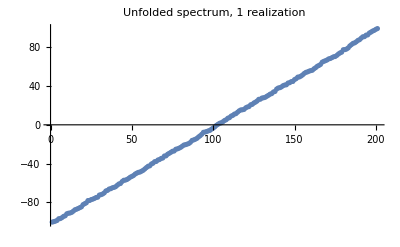

```mathematica
ListPlot[unfoldedSpectrum,PlotLabel->Style["Unfolded spectrum, 1 realization",20,Black]]
```

```mathematica
delta3[interval_]:=Module[{fit,residuals,intervalLength},intervalLength=Length[interval];
fit=FindFit[Transpose[{Range[intervalLength],interval}],a+b x,{a,b},x];
residuals=interval-(a+b Range[intervalLength]/. fit);
Total[residuals^2]/intervalLength];

calculateDelta3[spectrum_,l_]:=Module[{intervals},intervals=Table[Take[spectrum,{i,Min[i+l-1,Length[spectrum]]}],{i,1,Length[spectrum]-l+1}];
Mean[delta3/@intervals]];

lRange=Range[2,50,2];
delta3Values=Table[calculateDelta3[unfoldedSpectrum,l],{l,lRange}];
```

```mathematica
numberVariance[spectrum_,l_]:=Module[{counts},counts=Table[Length[Select[spectrum,#>=i&&#<i+l&]],{i,0,Max[spectrum]-l,l}];
Variance[counts]];
numberVarianceValues=Table[numberVariance[unfoldedSpectrum,l],{l,lRange}];
```

Variance::shlen: The argument {51} should have at least two elements.

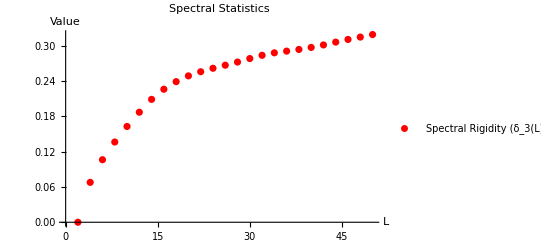

```mathematica
ListPlot[{Transpose[{lRange,delta3Values}]},PlotLegends->{"Spectral Rigidity (δ_3(L))","Number Variance (σ^2(L))"},PlotStyle->{Red,Blue},AxesLabel->{"L","Value"},PlotLabel->"Spectral Statistics"]
```

## QKT

```mathematica
J=200;
dim=J+1;
α=0.84;
τ=1;
p=50;
k=15.;
klist=RandomReal[{k-0.001,k+0.001},p];
```

```mathematica
matrices=ParallelTable[Floq[J,α,k,τ],{k,klist}];
matricesM=Table[k[[i,j]],{k,matrices},{i,1,2J+1,2},{j,1,2J+1,2}];
eigenvals=ParallelTable[Eigenvalues[i],{i,matricesM}];
args=Arg[eigenvals];
```

```mathematica
Histogram[Join@@args,{-Pi,Pi,2 Pi/40},PDF,PlotLabel->Style["Dim = "<>ToString[dim]<>", realizations = "<>ToString[p],Black,20]]
diffs=Join@@Map[Composition[Differences,Sort],args/(2 Pi) dim];
Show[Histogram[diffs,{0.1},PDF],Plot[WignerSurmisePDF[x,1],{x,0,3}],PlotLabel->Style["Dim = "<>ToString[dim]<>", realizations = "<>ToString[p],Black,20],PlotRange->All]
```

-Graphics-

-Graphics-

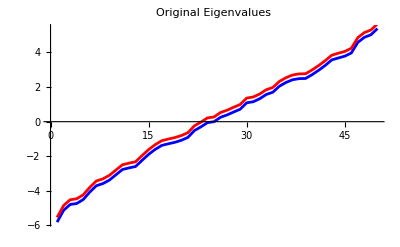

```mathematica
(*Number of matrix dimensions*)n=50;

(*Generate a random COE matrix (symmetric matrix)*)
coeMatrix=RandomReal[{-1,1},{n,n}];
coeMatrix=(coeMatrix+Transpose[coeMatrix])/2; (*Ensure symmetry*)

(*Compute eigenvalues*)
eigenvalues=Eigenvalues[coeMatrix];

(*Sort eigenvalues in ascending order*)
sortedEigenvalues=Sort[eigenvalues];

(*Compute the cumulative distribution function (CDF)*)
cdf=Table[i/n,{i,1,n}];

(*Compute the unfolding function:map eigenvalues to uniform distribution*)
unfoldedEigenvalues=Table[sortedEigenvalues[[i]]-sortedEigenvalues[[1]]/Norm[sortedEigenvalues,2],{i,n}];

(*Plot original vs unfolded eigenvalues*)
originalPlot=ListLinePlot[sortedEigenvalues,PlotRange->All,PlotStyle->Blue,PlotLabel->"Original Eigenvalues"];

unfoldedPlot=ListLinePlot[unfoldedEigenvalues,PlotRange->All,PlotStyle->Red,PlotLabel->"Unfolded Eigenvalues"];

(*Display the plots*)
Show[originalPlot,unfoldedPlot]
```